```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
```

Here, using cooperative specialization reaction diffusion equations when generalist average payoff exceeds average specialist payoff, we evaluate how the average frequency of generalist hosts changes in response to changes in the diffusion rate of other strategists.

First, we’ll vary symbiont diffusion rate, and hold the rate of diffusion of the other strategists constant:

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

General::stop: Further output of NDSolve::ibcinc will be suppressed during this calculation.

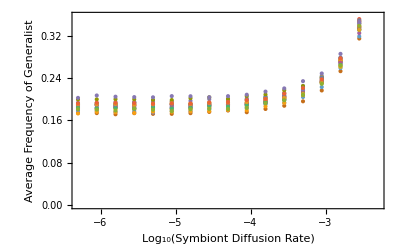

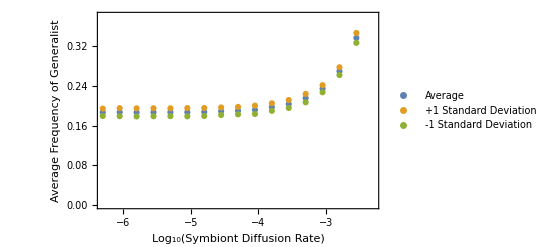

{{-2.30103,0.4540.013},{-2.55103,0.3370.010},{-2.80103,0.2700.008},{-3.05103,0.2340.007},{-3.30103,0.2150.008},{-3.55103,0.2040.008},{-3.80103,0.1970.008},{-4.05103,0.1920.008},{-4.30103,0.1900.008},{-4.55103,0.1890.008},{-4.80103,0.1870.008},{-5.05103,0.1870.008},{-5.30103,0.1870.008},{-5.55103,0.1870.008},{-5.80103,0.1870.008},{-6.05103,0.1870.008},{-6.30103,0.1870.007}}

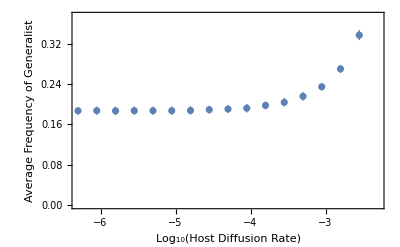

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
(*Generate Initial Conditions: *)
(*Size of domain*)l=40;
(*number of points*)pts=40;
groupedlist=Table[s10=RandomReal[{0,1},10000];
s20=1-u0;
v10i=RandomReal[{0,1},10000];
v20i=RandomReal[{0,1},10000];
vg0i=RandomReal[{0,1},10000];
vga=vg0i/(v10i+v20i+vg0i); 
v1a=v10i/(v10i+v20i+vg0i);
v2a=v20i/(v10i+v20i+vg0i);
(*Create a table of xy coordinates: *)
v10a=Flatten[Table[{x,y},{x,0,l,l/pts},{y,0,l,l/pts}]];
v20a=Flatten[Table[{x,y},{x,0,l,l/pts},{y,0,l,l/pts}]];
vg0a=Flatten[Table[{x,y},{x,0,l,l/pts},{y,0,l,l/pts}]];
s10a=Flatten[Table[{x,y},{x,0,l,l/pts},{y,0,l,l/pts}]];
s20a=Flatten[Table[{x,y},{x,0,l,l/pts},{y,0,l,l/pts}]];
(*Add normalized, random initial frequency of each strategist to this xy plane: *)
vg01b=Riffle[vg0a,vga,3];
vg01c=AppendTo[vg01b,Last[vga]];
vg0d=Partition[vg01c,3];
v10b=Riffle[v10a,v1a,3];
v01c=AppendTo[v10b,Last[v1a]];
v10d=Partition[v01c,3];
v20b=Riffle[v20a,v2a,3];
v02c=AppendTo[v20b,Last[v2a]];
v20d=Partition[v02c,3];
s10b=Riffle[s10a,v1a,3];
s01c=AppendTo[s10b,Last[v1a]];
s10d=Partition[s01c,3];
s20b=Riffle[s20a,v2a,3];
s02c=AppendTo[s20b,Last[v2a]];
s20d=Partition[s02c,3];
(*Use an interpolation function to rasterize: *)
v10=Interpolation[v10d,InterpolationOrder->0];
v20=Interpolation[v20d,InterpolationOrder->0];
vg0=Interpolation[vg0d,InterpolationOrder->0];
s10=Interpolation[s10d,InterpolationOrder->0];
s20=Interpolation[s20d,InterpolationOrder->0];

ClearAll[DVG,DV1,DV2,DS1,DS2];
Table[{Log10[DS1],
DV2=DV1=DVG=0.000005 ;
DS2=DS1;

tmax=1000;(*max time*)
(*numerical spatial resolution*)
sol2=NDSolve[{
(*Frequency of each strategist*)D[s1[x,y,t],t]==s1[x,y,t] (0.275 v1[x,y,t]+0.025 v2[x,y,t]-s1[x,y,t] (0.275 v1[x,y,t]+0.025 v2[x,y,t]+0.25 vg[x,y,t])-s2[x,y,t] (0.025 v1[x,y,t]+0.275 v2[x,y,t]+0.25 vg[x,y,t])+0.25 vg[x,y,t])+DS1*(D[s1[x,y,t],{x,2}]+D[s1[x,y,t],{y,2}]),
D[s2[x,y,t],t]==s2[x,y,t] (0.025 v1[x,y,t]+0.275 v2[x,y,t]-s1[x,y,t] (0.275 v1[x,y,t]+0.025 v2[x,y,t]+0.25 vg[x,y,t])-s2[x,y,t] (0.025 v1[x,y,t]+0.275 v2[x,y,t]+0.25 vg[x,y,t])+0.25 vg[x,y,t])+DS2*(D[s2[x,y,t],{x,2}]+D[s2[x,y,t],{y,2}]),
D[v1[x,y,t],t]==v1[x,y,t] (0.+0.025000000000000022 s1[x,y,t]-0.225 s2[x,y,t]-(0.025000000000000022 s1[x,y,t]-0.225 s2[x,y,t]) v1[x,y,t]-(-0.225 s1[x,y,t]+0.025000000000000022 s2[x,y,t]) v2[x,y,t])+DV1*(D[v1[x,y,t],{x,2}]+D[v1[x,y,t],{y,2}]),
D[v2[x,y,t],t]==v2[x,y,t] (0.-0.225 s1[x,y,t]+0.025000000000000022 s2[x,y,t]-(0.025000000000000022 s1[x,y,t]-0.225 s2[x,y,t]) v1[x,y,t]-(-0.225 s1[x,y,t]+0.025000000000000022 s2[x,y,t]) v2[x,y,t])+DV2*(D[v2[x,y,t],{x,2}]+D[v2[x,y,t],{y,2}]),
D[vg[x,y,t],t]==(0.-(0.025000000000000022 s1[x,y,t]-0.225 s2[x,y,t]) v1[x,y,t]-(-0.225 s1[x,y,t]+0.025000000000000022 s2[x,y,t]) v2[x,y,t]) vg[x,y,t]+DVG*(D[vg[x,y,t],{x,2}]+D[vg[x,y,t],{y,2}]),(*initial conditions*)v1[x,y,0]==v10[x,y],v2[x,y,0]==v20[x,y],vg[x,y,0]==vg0[x,y],s1[x,y,0]==s10[x,y],s2[x,y,0]==s20[x,y],
(*periodic boundary conditions*)v1[0,y,t]==v1[l,y,t],v2[0,y,t]==v2[l,y,t],vg[0,y,t]==vg[l,y,t],s1[0,y,t]==s1[l,y,t],s2[0,y,t]==s2[l,y,t],

v1[x,0,t]==v1[x,l,t],v2[x,0,t]==v2[x,l,t],vg[x,0,t]==vg[x,l,t],s1[x,0,t]==s1[x,l,t],s2[x,0,t]==s2[x,l,t]},
{v1,v2,vg,s1,s2},{t,0,tmax},{x,0,l},{y,0,l},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->pts,"MaxPoints"->pts}}];
solvg=Flatten[sol2][[3]];
sols1=Flatten[sol2][[4]];
sols2=Flatten[sol2][[5]];
solv1=Flatten[sol2][[1]];
solv2=Flatten[sol2][[2]];

solvgtmax=solvg/.t-> tmax;
tmaxvaluesvg=InterpolatingFunctionValuesOnGrid[vg/.solvgtmax];
avgvg=Mean[Flatten[tmaxvaluesvg]]}
,{DS1,Table[5*10^-i,{i,3,7,0.25}]  }],20];
ListPlot[groupedlist,Axes->False,Frame->{{True,False},{True,False}},FrameTicks->All,FrameLabel-> {{"Average Frequency of Generalist",None},{"Log_10(Symbiont Diffusion Rate)",None}}]

l1=Flatten[groupedlist,1];
mean=GroupBy[l1,First-> Last, Mean];
stdev=GroupBy[l1,First-> Last, StandardDeviation];

ListPlot[{mean,mean+stdev,mean-stdev},Axes->False,PlotLegends -> {"Average","+1 Standard Deviation", "-1 Standard Deviation"} ,Frame->{{True,False},{True,False}},FrameTicks->All,FrameLabel-> {{"Average Frequency of Generalist",None},{"Log_10(Symbiont Diffusion Rate)",None}}]
data1=KeyValueMap[List]@GroupBy[l1,First->Last,Around];
ListPlot[data1,Axes->False ,Frame->{{True,False},{True,False}},FrameTicks->All,FrameLabel-> {{"Average Frequency of Generalist",None},{"Log_10(Host Diffusion Rate)",None}}]
```

Now, we’ll vary the diffusion rate of all hosts, and hold the diffusion rate of symbionts constant:

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

General::stop: Further output of NDSolve::ibcinc will be suppressed during this calculation.

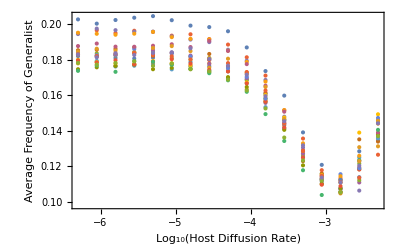

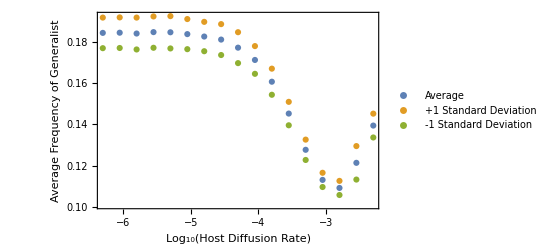

{{-2.30103,0.1390.006},{-2.55103,0.1210.008},{-2.80103,0.10920.0034},{-3.05103,0.11310.0035},{-3.30103,0.1280.005},{-3.55103,0.1450.006},{-3.80103,0.1610.006},{-4.05103,0.1710.007},{-4.30103,0.1770.007},{-4.55103,0.1810.007},{-4.80103,0.1830.007},{-5.05103,0.1840.007},{-5.30103,0.1850.008},{-5.55103,0.1850.008},{-5.80103,0.1840.008},{-6.05103,0.1840.007},{-6.30103,0.1840.007}}

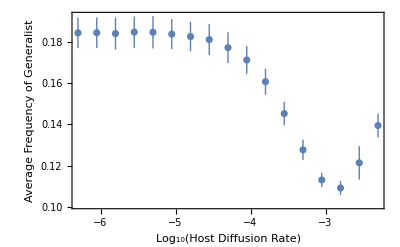

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
(*Generate Initial Conditions: *)
(*Size of domain*)l=40;
(*number of points*)pts=40;
groupedlist=Table[s10=RandomReal[{0,1},10000];
s20=1-u0;
v10i=RandomReal[{0,1},10000];
v20i=RandomReal[{0,1},10000];
vg0i=RandomReal[{0,1},10000];
vga=vg0i/(v10i+v20i+vg0i); 
v1a=v10i/(v10i+v20i+vg0i);
v2a=v20i/(v10i+v20i+vg0i);
(*Create a table of xy coordinates: *)
v10a=Flatten[Table[{x,y},{x,0,l,l/pts},{y,0,l,l/pts}]];
v20a=Flatten[Table[{x,y},{x,0,l,l/pts},{y,0,l,l/pts}]];
vg0a=Flatten[Table[{x,y},{x,0,l,l/pts},{y,0,l,l/pts}]];
s10a=Flatten[Table[{x,y},{x,0,l,l/pts},{y,0,l,l/pts}]];
s20a=Flatten[Table[{x,y},{x,0,l,l/pts},{y,0,l,l/pts}]];
(*Add normalized, random initial frequency of each strategist to this xy plane: *)
vg01b=Riffle[vg0a,vga,3];
vg01c=AppendTo[vg01b,Last[vga]];
vg0d=Partition[vg01c,3];
v10b=Riffle[v10a,v1a,3];
v01c=AppendTo[v10b,Last[v1a]];
v10d=Partition[v01c,3];
v20b=Riffle[v20a,v2a,3];
v02c=AppendTo[v20b,Last[v2a]];
v20d=Partition[v02c,3];
s10b=Riffle[s10a,v1a,3];
s01c=AppendTo[s10b,Last[v1a]];
s10d=Partition[s01c,3];
s20b=Riffle[s20a,v2a,3];
s02c=AppendTo[s20b,Last[v2a]];
s20d=Partition[s02c,3];
(*Use an interpolation function to rasterize: *)
v10=Interpolation[v10d,InterpolationOrder->0];
v20=Interpolation[v20d,InterpolationOrder->0];
vg0=Interpolation[vg0d,InterpolationOrder->0];
s10=Interpolation[s10d,InterpolationOrder->0];
s20=Interpolation[s20d,InterpolationOrder->0];

ClearAll[DVG,DV1,DV2,DS1,DS2];
Table[{Log10[DVG],
DV2=DV1=DVG ;
DS2=DS1=0.000005;

tmax=1000;(*max time*)
(*numerical spatial resolution*)
sol2=NDSolve[{
(*Frequency of each strategist*)D[s1[x,y,t],t]==s1[x,y,t] (0.275 v1[x,y,t]+0.025 v2[x,y,t]-s1[x,y,t] (0.275 v1[x,y,t]+0.025 v2[x,y,t]+0.25 vg[x,y,t])-s2[x,y,t] (0.025 v1[x,y,t]+0.275 v2[x,y,t]+0.25 vg[x,y,t])+0.25 vg[x,y,t])+DS1*(D[s1[x,y,t],{x,2}]+D[s1[x,y,t],{y,2}]),
D[s2[x,y,t],t]==s2[x,y,t] (0.025 v1[x,y,t]+0.275 v2[x,y,t]-s1[x,y,t] (0.275 v1[x,y,t]+0.025 v2[x,y,t]+0.25 vg[x,y,t])-s2[x,y,t] (0.025 v1[x,y,t]+0.275 v2[x,y,t]+0.25 vg[x,y,t])+0.25 vg[x,y,t])+DS2*(D[s2[x,y,t],{x,2}]+D[s2[x,y,t],{y,2}]),
D[v1[x,y,t],t]==v1[x,y,t] (0.+0.025000000000000022 s1[x,y,t]-0.225 s2[x,y,t]-(0.025000000000000022 s1[x,y,t]-0.225 s2[x,y,t]) v1[x,y,t]-(-0.225 s1[x,y,t]+0.025000000000000022 s2[x,y,t]) v2[x,y,t])+DV1*(D[v1[x,y,t],{x,2}]+D[v1[x,y,t],{y,2}]),
D[v2[x,y,t],t]==v2[x,y,t] (0.-0.225 s1[x,y,t]+0.025000000000000022 s2[x,y,t]-(0.025000000000000022 s1[x,y,t]-0.225 s2[x,y,t]) v1[x,y,t]-(-0.225 s1[x,y,t]+0.025000000000000022 s2[x,y,t]) v2[x,y,t])+DV2*(D[v2[x,y,t],{x,2}]+D[v2[x,y,t],{y,2}]),
D[vg[x,y,t],t]==(0.-(0.025000000000000022 s1[x,y,t]-0.225 s2[x,y,t]) v1[x,y,t]-(-0.225 s1[x,y,t]+0.025000000000000022 s2[x,y,t]) v2[x,y,t]) vg[x,y,t]+DVG*(D[vg[x,y,t],{x,2}]+D[vg[x,y,t],{y,2}]),(*initial conditions*)v1[x,y,0]==v10[x,y],v2[x,y,0]==v20[x,y],vg[x,y,0]==vg0[x,y],s1[x,y,0]==s10[x,y],s2[x,y,0]==s20[x,y],
(*periodic boundary conditions*)v1[0,y,t]==v1[l,y,t],v2[0,y,t]==v2[l,y,t],vg[0,y,t]==vg[l,y,t],s1[0,y,t]==s1[l,y,t],s2[0,y,t]==s2[l,y,t],

v1[x,0,t]==v1[x,l,t],v2[x,0,t]==v2[x,l,t],vg[x,0,t]==vg[x,l,t],s1[x,0,t]==s1[x,l,t],s2[x,0,t]==s2[x,l,t]},
{v1,v2,vg,s1,s2},{t,0,tmax},{x,0,l},{y,0,l},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->pts,"MaxPoints"->pts}}];
solvg=Flatten[sol2][[3]];
sols1=Flatten[sol2][[4]];
sols2=Flatten[sol2][[5]];
solv1=Flatten[sol2][[1]];
solv2=Flatten[sol2][[2]];

solvgtmax=solvg/.t-> tmax;
tmaxvaluesvg=InterpolatingFunctionValuesOnGrid[vg/.solvgtmax];
avgvg=Mean[Flatten[tmaxvaluesvg]]}
,{DVG,Table[5*10^-i,{i,3,7,0.25}]  }],20];
ListPlot[groupedlist,Axes->False,Frame->{{True,False},{True,False}},FrameTicks->All,FrameLabel-> {{"Average Frequency of Generalist",None},{"Log_10(Host Diffusion Rate)",None}}]

l2=Flatten[groupedlist,1];
mean=GroupBy[l2,First-> Last, Mean];
stdev=GroupBy[l2,First-> Last, StandardDeviation];

ListPlot[{mean,mean+stdev,mean-stdev},Axes->False,PlotLegends -> {"Average","+1 Standard Deviation", "-1 Standard Deviation"} ,Frame->{{True,False},{True,False}},FrameTicks->All,FrameLabel-> {{"Average Frequency of Generalist",None},{"Log_10(Host Diffusion Rate)",None}}]
data2=KeyValueMap[List]@GroupBy[l2,First->Last,Around];
ListPlot[data2,Axes->False ,Frame->{{True,False},{True,False}},FrameTicks->All,FrameLabel-> {{"Average Frequency of Generalist",None},{"Log_10(Host Diffusion Rate)",None}}]
```

Finally we’ll vary the diffusion rate of all strategists:

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

NDSolve::eerri: Warning: estimated initial error on the specified spatial grid in the direction of independent variable x exceeds prescribed error tolerance.

NDSolve::eerri: Warning: estimated initial error on the specified spatial grid in the direction of independent variable y exceeds prescribed error tolerance.

NDSolve::ibcinc: Warning: boundary and initial conditions are inconsistent.

General::stop: Further output of NDSolve::ibcinc will be suppressed during this calculation.

NDSolve::eerri: Warning: estimated initial error on the specified spatial grid in the direction of independent variable x exceeds prescribed error tolerance.

General::stop: Further output of NDSolve::eerri will be suppressed during this calculation.

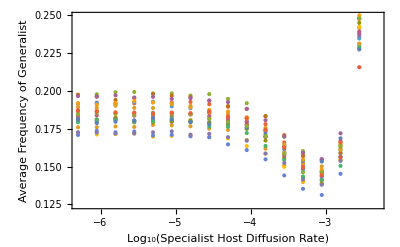

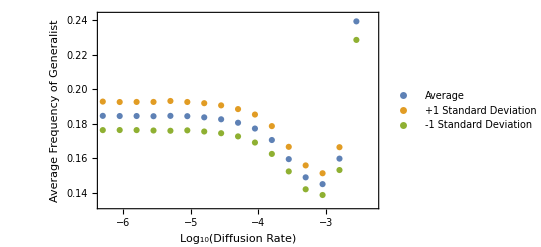

GroupBy::list1: The argument 40 is not a valid list of Associations or rules or lists of rules.

KeyValueMap::invak: The argument GroupBy[40,First→Last,Around] is not a valid Association.

KeyValueMap[List][GroupBy[40,First→Last,Around]]

GroupBy::list1: The argument 40. is not a valid list of Associations or rules or lists of rules.

KeyValueMap::invak: The argument GroupBy[40.,First→Last,Around] is not a valid Association.

GroupBy::list1: The argument 40. is not a valid list of Associations or rules or lists of rules.

KeyValueMap::invak: The argument GroupBy[40.,First→Last,Around] is not a valid Association.

GroupBy::list1: The argument 40. is not a valid list of Associations or rules or lists of rules.

General::stop: Further output of GroupBy::list1 will be suppressed during this calculation.

KeyValueMap::invak: The argument GroupBy[40.,First→Last,Around] is not a valid Association.

General::stop: Further output of KeyValueMap::invak will be suppressed during this calculation.

ListPlot::lpn: KeyValueMap[List][GroupBy[40.,First→Last,Around]] is not a list of numbers or pairs of numbers.

ListPlot[KeyValueMap[List][GroupBy[40,First→Last,Around]],Axes→False,PlotRange→{0.125,0.255},Frame→{{True,False},{True,False}},FrameTicks→All,FrameLabel→{{Average Frequency of Generalist,None},{Log_10(Diffusion Rate),None}}]

```mathematica
Needs["DifferentialEquations`InterpolatingFunctionAnatomy`"];
(*Generate Initial Conditions: *)
(*Size of domain*)l=40;
(*number of points*)pts=40;
groupedlist=Table[s10=RandomReal[{0,1},10000];
s20=1-u0;
v10i=RandomReal[{0,1},10000];
v20i=RandomReal[{0,1},10000];
vg0i=RandomReal[{0,1},10000];
vga=vg0i/(v10i+v20i+vg0i); 
v1a=v10i/(v10i+v20i+vg0i);
v2a=v20i/(v10i+v20i+vg0i);
(*Create a table of xy coordinates: *)
v10a=Flatten[Table[{x,y},{x,0,l,l/pts},{y,0,l,l/pts}]];
v20a=Flatten[Table[{x,y},{x,0,l,l/pts},{y,0,l,l/pts}]];
vg0a=Flatten[Table[{x,y},{x,0,l,l/pts},{y,0,l,l/pts}]];
s10a=Flatten[Table[{x,y},{x,0,l,l/pts},{y,0,l,l/pts}]];
s20a=Flatten[Table[{x,y},{x,0,l,l/pts},{y,0,l,l/pts}]];
(*Add normalized, random initial frequency of each strategist to this xy plane: *)
vg01b=Riffle[vg0a,vga,3];
vg01c=AppendTo[vg01b,Last[vga]];
vg0d=Partition[vg01c,3];
v10b=Riffle[v10a,v1a,3];
v01c=AppendTo[v10b,Last[v1a]];
v10d=Partition[v01c,3];
v20b=Riffle[v20a,v2a,3];
v02c=AppendTo[v20b,Last[v2a]];
v20d=Partition[v02c,3];
s10b=Riffle[s10a,v1a,3];
s01c=AppendTo[s10b,Last[v1a]];
s10d=Partition[s01c,3];
s20b=Riffle[s20a,v2a,3];
s02c=AppendTo[s20b,Last[v2a]];
s20d=Partition[s02c,3];
(*Use an interpolation function to rasterize: *)
v10=Interpolation[v10d,InterpolationOrder->0];
v20=Interpolation[v20d,InterpolationOrder->0];
vg0=Interpolation[vg0d,InterpolationOrder->0];
s10=Interpolation[s10d,InterpolationOrder->0];
s20=Interpolation[s20d,InterpolationOrder->0];

ClearAll[DVG,DV1,DV2,DS1,DS2];
Table[{Log10[DV1],
DV2=DVG =DS1=DS2=DV1;

tmax=1000;(*max time*)
(*numerical spatial resolution*)
sol2=NDSolve[{
(*Frequency of each strategist*)D[s1[x,y,t],t]==s1[x,y,t] (0.275 v1[x,y,t]+0.025 v2[x,y,t]-s1[x,y,t] (0.275 v1[x,y,t]+0.025 v2[x,y,t]+0.25 vg[x,y,t])-s2[x,y,t] (0.025 v1[x,y,t]+0.275 v2[x,y,t]+0.25 vg[x,y,t])+0.25 vg[x,y,t])+DS1*(D[s1[x,y,t],{x,2}]+D[s1[x,y,t],{y,2}]),
D[s2[x,y,t],t]==s2[x,y,t] (0.025 v1[x,y,t]+0.275 v2[x,y,t]-s1[x,y,t] (0.275 v1[x,y,t]+0.025 v2[x,y,t]+0.25 vg[x,y,t])-s2[x,y,t] (0.025 v1[x,y,t]+0.275 v2[x,y,t]+0.25 vg[x,y,t])+0.25 vg[x,y,t])+DS2*(D[s2[x,y,t],{x,2}]+D[s2[x,y,t],{y,2}]),
D[v1[x,y,t],t]==v1[x,y,t] (0.+0.025000000000000022 s1[x,y,t]-0.225 s2[x,y,t]-(0.025000000000000022 s1[x,y,t]-0.225 s2[x,y,t]) v1[x,y,t]-(-0.225 s1[x,y,t]+0.025000000000000022 s2[x,y,t]) v2[x,y,t])+DV1*(D[v1[x,y,t],{x,2}]+D[v1[x,y,t],{y,2}]),
D[v2[x,y,t],t]==v2[x,y,t] (0.-0.225 s1[x,y,t]+0.025000000000000022 s2[x,y,t]-(0.025000000000000022 s1[x,y,t]-0.225 s2[x,y,t]) v1[x,y,t]-(-0.225 s1[x,y,t]+0.025000000000000022 s2[x,y,t]) v2[x,y,t])+DV2*(D[v2[x,y,t],{x,2}]+D[v2[x,y,t],{y,2}]),
D[vg[x,y,t],t]==(0.-(0.025000000000000022 s1[x,y,t]-0.225 s2[x,y,t]) v1[x,y,t]-(-0.225 s1[x,y,t]+0.025000000000000022 s2[x,y,t]) v2[x,y,t]) vg[x,y,t]+DVG*(D[vg[x,y,t],{x,2}]+D[vg[x,y,t],{y,2}]),(*initial conditions*)v1[x,y,0]==v10[x,y],v2[x,y,0]==v20[x,y],vg[x,y,0]==vg0[x,y],s1[x,y,0]==s10[x,y],s2[x,y,0]==s20[x,y],
(*periodic boundary conditions*)v1[0,y,t]==v1[l,y,t],v2[0,y,t]==v2[l,y,t],vg[0,y,t]==vg[l,y,t],s1[0,y,t]==s1[l,y,t],s2[0,y,t]==s2[l,y,t],

v1[x,0,t]==v1[x,l,t],v2[x,0,t]==v2[x,l,t],vg[x,0,t]==vg[x,l,t],s1[x,0,t]==s1[x,l,t],s2[x,0,t]==s2[x,l,t]},
{v1,v2,vg,s1,s2},{t,0,tmax},{x,0,l},{y,0,l},Method->{"MethodOfLines","SpatialDiscretization"->{"TensorProductGrid","MinPoints"->pts,"MaxPoints"->pts}}];
solvg=Flatten[sol2][[3]];
sols1=Flatten[sol2][[4]];
sols2=Flatten[sol2][[5]];
solv1=Flatten[sol2][[1]];
solv2=Flatten[sol2][[2]];

solvgtmax=solvg/.t-> tmax;
tmaxvaluesvg=InterpolatingFunctionValuesOnGrid[vg/.solvgtmax];
avgvg=Mean[Flatten[tmaxvaluesvg]]}
,{DV1,Table[5*10^-i,{i,3,7,0.25}]  }],20];
ListPlot[groupedlist,Axes->False,Frame->{{True,False},{True,False}},FrameTicks->All,FrameLabel-> {{"Average Frequency of Generalist",None},{"Log_10(Specialist Host Diffusion Rate)",None}}]

l3=Flatten[groupedlist,1];
mean=GroupBy[l3,First-> Last, Mean];
stdev=GroupBy[l3,First-> Last, StandardDeviation];

ListPlot[{mean,mean+stdev,mean-stdev},Axes->False,PlotLegends -> {"Average","+1 Standard Deviation", "-1 Standard Deviation"} ,Frame->{{True,False},{True,False}},FrameTicks->All,FrameLabel-> {{"Average Frequency of Generalist",None},{"Log_10(Diffusion Rate)",None}}]
data3=KeyValueMap[List]@GroupBy[l3,First->Last,Around];
ListPlot[data3,Axes->False ,PlotRange-> {0.125,0.255},Frame->{{True,False},{True,False}},FrameTicks->All,FrameLabel-> {{"Average Frequency of Generalist",None},{"Log_10(Diffusion Rate)",None}}]
```